# Computação Natural - Aula 03 - Redes Neurais Artificiais (alguns exemplos)

## Funções

### Função degrau

```mathematica
StepFunction[x_]:=If[x≥0,1.,0.];
```

### McCulloch & Pitts

```mathematica
McCullochPittsPlot2D[theta_,f_]:=ContourPlot[f[x1+x2+theta],{x1,-1,1},{x2,-1,1},PlotLegends->Automatic];
McCullochPittsPlot2D[theta_,f_,{xi_,xf_},{yi_,yf_}]:=RegionPlot[f[x1+x2+theta],{x1,xi,xf},{x2,yi,yf},PlotLegends->Automatic];
```

### Perceptron Simples

```mathematica
Perceptron[x_List,w_List,b_,f_]:=f[Total[x*w]+b];
```

```mathematica
TrainPerceptron[inputs_List,outputs_List,f_,maxit_Integer,eps_,alpha_]:=Module[{w=Table[RandomReal[{-0.1,0.1}],Length[inputs⟦1⟧]],b=RandomReal[{-0.1,0.1}],i=1,e=Infinity},
While[i≤maxit&&e>eps,
e=0;
For[j=1,j≤Length[inputs],j++,
With[{ej=(outputs⟦j⟧-Perceptron[inputs⟦j⟧,w,b,f])},
w=w+alpha*ej*inputs⟦j⟧;
b=b+alpha*ej;
e=e+ej^2
];
];
i++;
];
{w,b,i,e}
];
```

```mathematica
TrainPerceptron[{{0,0},{0,1},{1,0},{1,1}},{0,0,0,1},If[#≥0,1,0]&,100,0.001,0.1]
```

{{0.160447,0.129245},-0.258815,7,0}

```mathematica
Perceptron[#,%120⟦1⟧,%120⟦2⟧,StepFunction]&/@{{0,0},{0,1},{1,0},{1,1}}
```

{0.,0.,0.,1.}

### Perceptron de múltiplas saídas

```mathematica
MOPerceptron[x_List,W_List,b_List,f_List]:=With[{L=Length[W]},Table[f⟦i⟧[Dot[W⟦i⟧,x]+b⟦i⟧],{i,1,L}]];
```

```mathematica
MOPerceptron[{0,0},{{0.1,-0.1},{-0.1,0.05}},{StepFunction,StepFunction}]
```

```mathematica
TrainMOPerceptron[inputs_List,outputs_List,f_List,maxit_Integer,eps_,alpha_]:=
Module[{W=Table[RandomReal[{-0.1,0.1}],Length[outputs⟦1⟧],Length[inputs⟦1⟧]],B=Table[RandomReal[{-0.1,0.1}],Length[outputs⟦1⟧]],i=1,e=Infinity},
While[i≤maxit&&e>eps,
e=0;
For[j=1,j≤Length[inputs],j++,
With[{ej=(outputs⟦j⟧-MOPerceptron[inputs⟦j⟧,W,B,f])},
W=W+alpha*Dot[Transpose[{ej}],{inputs⟦j⟧}];
B=B+alpha*ej;
e=e+Total[ej^2]/Length[ej];
];
];
e=e/Length[inputs];
i++;
];
{W,B,i-1,e}
]
```

### Treinamento competitivo

```mathematica
CompetitiveTraining[inputs_List,N_,maxit_Integer,alpha_]:=Module[{W=Table[RandomReal[{-0.1,0.1}],N,Length[inputs⟦1⟧]],i=1},
While[i≤maxit,
For[j=1,j≤Length[inputs],j++,
With[{dists=Norm[#]&/@Table[inputs⟦j⟧-W⟦k⟧,{k,1,N}]},
With[{pos=Flatten[Position[dists,Min[dists]]]⟦1⟧},
W⟦pos⟧+=alpha*(inputs⟦j⟧-W⟦pos⟧)
];
];
];
i++
];
W
];
```

### Dados

```mathematica
RelatorioResultados[entradas_,saidasesperadas_,saidasreais_]:=With[{acertos=Table[If[saidasesperadas⟦i⟧==saidasreais⟦i⟧,1,0],{i,1,Length[saidasreais]}]},
{N[Total[acertos]/Length[entradas]],With[{pos=Flatten[Position[acertos,0]]},Transpose[{entradas⟦pos⟧,saidasreais⟦pos⟧,saidasesperadas⟦pos⟧}]]}
];
```

```mathematica
DiscretizaSaida[x_]:=With[{M=Max[x]},Table[If[x⟦i⟧==M,1,0],{i,1,Length[x]}]];
```

## Exemplos

### Exemplo 1: McCulloch & Pitts com diversos valores de θ:

```mathematica
ListAnimate[Grid[{{#},{McCullochPittsPlot2D[#,StepFunction]}}]&/@Range[-2,2,0.1]]
```

### Exemplo 2: “McCulloch & Pitts” generalizado com diferentes funções de ativação e diversos valores de θ:

#### Função linear

```mathematica
ListAnimate[Table[McCullochPittsPlot2D[theta,(#)&],{theta,Range[-2,2,0.1]}]]
```

#### Função logística

```mathematica
ListAnimate[Table[McCullochPittsPlot2D[theta,(1/(1+Exp[-#]))&],{theta,Range[-2,2,0.1]}]]
```

### Exemplo 3: Perceptron simples com bias = 0, valores de peso variando entre -2 e 2 e função de ativação degrau.

```mathematica
Manipulate[ContourPlot[Perceptron[{x1,x2},{w1,w2},0,StepFunction],{x1,0,1},{x2,0,1}],{w1,Range[-2,2,0.1],ControlType->Slider},{w2,Range[-2,2,0.1],ControlType->Slider}]
```

### Exemplo 4: Perceptron simples com bias = 0, valores de peso variando entre -2 e 2 e função de ativação logística.

```mathematica
Manipulate[DensityPlot[Perceptron[{x1,x2},{w1,w2},0,(1/(1+Exp[-#]))&],{x1,0,1},{x2,0,1}],{w1,Range[-2,2,0.1],ControlType->Slider},{w2,Range[-2,2,0.1],ControlType->Slider}]
```

```mathematica
Perceptron[{1,0},{Ex3w1,Ex3w2},0,StepFunction]
```

1.

### Exemplo 5: Treinamento de perceptron simples para simulação da função AND

```mathematica
entradasEx5={{0,0},{0,1},{1,0},{1,1}};
saidasEx5={0,0,0,1};
```

```mathematica
treinamentoEx5=TrainPerceptron[entradasEx5,saidasEx5,StepFunction,100,0.001,0.1]
```

```mathematica
MatrixForm[{#,Perceptron[#,treinamentoEx5⟦1⟧,treinamentoEx5⟦2⟧,StepFunction]}&/@entradasEx5]
```

### Exemplo 6: Treinamento de perceptron simples de múltipla saída para simulação da função AND

```mathematica
entradasEx6={{0,0},{0,1},{1,0},{1,1}};
saidasEx6={{1,0},{1,0},{1,0},{0,1}};
```

```mathematica
treinamentoEx6=TrainMOPerceptron[entradasEx6,saidasEx6,{StepFunction,StepFunction},100,0.001,0.1]
```

```mathematica
MatrixForm[{#,MOPerceptron[#,treinamentoEx6⟦1⟧,treinamentoEx6⟦2⟧,{StepFunction,StepFunction}]}&/@entradasEx6]
```

### Exemplo 7: Treinamento de perceptron simples de múltipla saída para classificação de um conjunto de dados sintéticos com três clusters

```mathematica
Ex7Data=Flatten[{Table[{0+RandomReal[{-0.2,0.2}],0+RandomReal[{-0.2,0.2}]},100],Table[{0.5+RandomReal[{-0.2,0.2}],0.5+RandomReal[{-0.2,0.2}]},100],Table[{1+RandomReal[{-0.2,0.2}],0+RandomReal[{-0.2,0.2}]},100]},1];
ListPlot[Ex7Data]
```

```mathematica
entradasEx7=Ex7Data;
saidasEx7=Flatten[{Table[{1,0,0},100],Table[{0,1,0},100],Table[{0,0,1},100]},1];
```

```mathematica
treinamentoEx7=TrainMOPerceptron[entradasEx7,saidasEx7,{StepFunction,StepFunction,StepFunction},1000,0.001,0.1]
```

```mathematica
MatrixForm[{#,MOPerceptron[#,treinamentoEx7⟦1⟧,treinamentoEx7⟦2⟧,{StepFunction,StepFunction,StepFunction}]}&/@entradasEx7]
```

```mathematica
testeEx7=Flatten[{Table[{0+RandomReal[{-0.2,0.2}],0+RandomReal[{-0.2,0.2}]},10],Table[{0.5+RandomReal[{-0.2,0.2}],0.5+RandomReal[{-0.2,0.2}]},10],Table[{1+RandomReal[{-0.2,0.2}],0+RandomReal[{-0.2,0.2}]},10]},1]
```

```mathematica
MatrixForm[{#,MOPerceptron[#,treinamentoEx7⟦1⟧,treinamentoEx7⟦2⟧,{StepFunction,StepFunction,StepFunction}]}&/@testeEx7]
```

### Exemplo 8: Treinamento de perceptron simples de múltipla saída para classificação de um conjunto de dados sintéticos com três clusters, mas mais sobrepostos

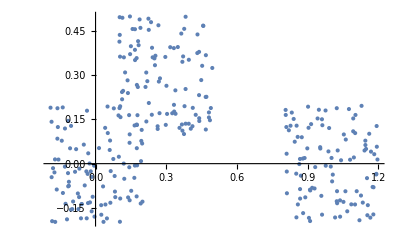

```mathematica
Ex8Data=Flatten[{Table[{0+RandomReal[{-0.2,0.2}],0+RandomReal[{-0.2,0.2}]},100],Table[{0.3+RandomReal[{-0.2,0.2}],0.3+RandomReal[{-0.2,0.2}]},100],Table[{1+RandomReal[{-0.2,0.2}],0+RandomReal[{-0.2,0.2}]},100]},1];
ListPlot[Ex8Data]
```

```mathematica
entradasEx8=Ex8Data;
saidasEx8=Flatten[{Table[{1,0,0},100],Table[{0,1,0},100],Table[{0,0,1},100]},1];
```

```mathematica
treinamentoEx8=TrainMOPerceptron[entradasEx8,saidasEx8,{StepFunction,StepFunction,StepFunction},1000,0.001,0.1]
```

```mathematica
saidasredeEx8={#,MOPerceptron[#,treinamentoEx8⟦1⟧,treinamentoEx8⟦2⟧,{StepFunction,StepFunction,StepFunction}]}&/@entradasEx8;
MatrixForm[saidasredeEx8]
```

```mathematica
RelatorioResultados[entradasEx8,saidasEx8,#⟦2⟧&/@saidasredeEx8]
```

### Exemplo 9: Exemplo 8, mas utilizando uma função logística

```mathematica
entradasEx9=Ex8Data;
saidasEx9=Flatten[{Table[{1,0,0},100],Table[{0,1,0},100],Table[{0,0,1},100]},1];
```

```mathematica
treinamentoEx9=TrainMOPerceptron[entradasEx9,saidasEx9,{(1/(1+Exp[-#]))&,(1/(1+Exp[-#]))&,(1/(1+Exp[-#]))&},1000,0.001,0.1]
```

```mathematica
saidasredeEx9={#,MOPerceptron[#,treinamentoEx9⟦1⟧,treinamentoEx9⟦2⟧,{(1/(1+Exp[-#]))&,(1/(1+Exp[-#]))&,(1/(1+Exp[-#]))&}]}&/@entradasEx9;
MatrixForm[saidasredeEx9]
```

```mathematica
saidasredeEx9disc=DiscretizaSaida[#]&/@Transpose[saidasredeEx9]⟦2⟧
```

```mathematica
RelatorioResultados[entradasEx9,saidasEx9,saidasredeEx9disc]
```

### Exemplo 10: Exemplo 8, mas com treinamento competitivo

```mathematica
entradasEx10=Ex8Data;
saidasEx10=Flatten[{Table[{1,0,0},100],Table[{0,1,0},100],Table[{0,0,1},100]},1];
```

```mathematica
treinamentoEx10=CompetitiveTraining[entradasEx10,3,100,0.1]
```

```mathematica
ListPlot[{entradasEx10⟦1;;100⟧,entradasEx10⟦101;;200⟧,entradasEx10⟦201;;300⟧,{treinamentoEx10⟦1⟧,treinamentoEx10⟦2⟧,treinamentoEx10⟦3⟧}}]
```